```mathematica
(*firstorder RMS approximation model *)
(* Souces 1) P-25:Inter-Grey-Level Response Times of a Liquid Crystal Display *)
(*        2) LCD RESPONSE TIME ESTIMATION, Adam et al. *)


(*Todo:
Gamma correction for grey->grey level dependece 
Better transmission vs internal voltage fit
 (slightly higher than it should be around 1-1.5Volt)
Transistor rise/fall times (including overdrive)
Fix overdrive? (overdrive at voltage or transmission space)
Other backlight behavoirs (CCFL etc.)*)

(* Variables *)
ContrastRatio := 200.0;
Transmission := 0.9;
PixelSpeed  :=0.0029;
Persistence :=0.006;
PersistenceDelay:=0.004;
FrameRate = 100;
PWMFrequency = 500;
Brightness = 0.5;
MaxVoltage =4.9; (* Transistor/Pixel rail voltage *)
OverdriveFactor= 0.25; (* Percent Overdrive*)

(* Definitions *)
T[V_]:=(1-Tanh[2V-4])/2(*Roungh Transmission vs internal voltage fit*)
V[T_]:=1/2 (4+ArcTanh[1-2 T]) (*Inverse of the above*)
Vbright = V[Transmission];
Vdark = V[Transmission/ContrastRatio];
PersistenceDutyCycle = Persistence*FrameRate;

(* Pixel Response, RMS model*)
StepResponse[t_,τ_]:=Piecewise[{{√(1-ⅇ^(-t/τ)), 0<t<10τ}, {1, True}}](*Windowed to 5 Tau*)  
ImpulseResponse[t_,τ_]=Evaluate@D[StepResponse[t,τ],t];

(*GTG correction, from second paper*)
Lh[t_]:=Max[Abs[T[Vextern[t-1/FrameRate]]],Abs[T[Vextern[t]]]](*Higher Grey level*)
Ll[t_]:=Min[Abs[T[Vextern[t-1/FrameRate]]],Abs[T[Vextern[t]]]] (*Lower Grey level*)
Delta[t_]:=Ll[t]/Lh[t];
τ[t_]:=PixelSpeed/(4 Log[3])Log[1+16/(1.8*Delta[t]+0.2)](*GTG correction*)

(*Input Signal*)
Signal[t_]:=UnitBox[FrameRate t-0.5]+UnitBox[FrameRate t-2.5]+1/2 UnitBox[FrameRate t-3.5]

(*Overdrive Algorithm*)
Vextern[t_]:=V[Transmission*Signal[t]+Transmission/ContrastRatio] (*no overdrive*)
FrameTime[t_]:=1/FrameRate Mod[ FrameRate t,1]

Overdrive[t_]:=Piecewise[{{0, FrameTime[t]==0}, {√(Max[Vextern[t]^2-Vextern[t-1/FrameRate]^2*ⅇ^((-FrameTime[t])/τ[t]),0]/(1-ⅇ^((-FrameTime[t])/τ[t]))), True}}]
Voverdrive[t_]:=Min[OverdriveFactor*Overdrive[t]+(1-OverdriveFactor)*Vextern[t],MaxVoltage]

(*Persistence and PWM simulation*)
DutyWave[t_,Duty_]:=Piecewise[{{SquareWave[{1,0},t-0.5]*SquareWave[{1,0},t-Duty], 0<=Duty<=0.5}, {Max[SquareWave[{1,0},t-0.5],SquareWave[{1,0},t-Duty]], 0.5<Duty<1}, {1, True}}]

(*Output, convolution*)
Vpixel[t_]:=Evaluate@NIntegrate[ImpulseResponse[s,τ[t]]*Voverdrive[t-s],{s,0,0,5*PixelSpeed},MaxRecursion->6]//Quiet
Tpixel[t_]:= T[Vpixel[t]]
```

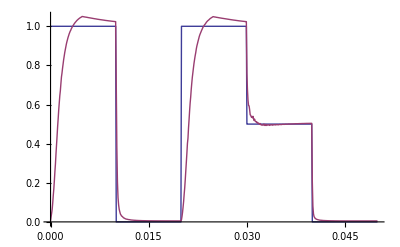

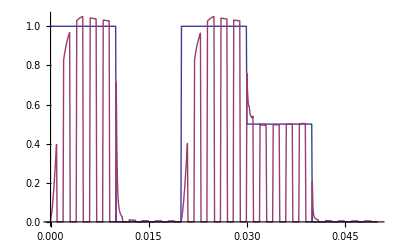

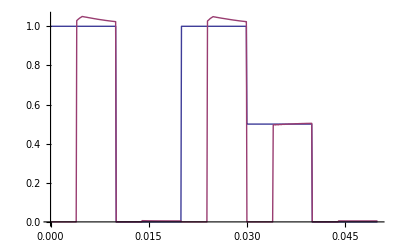

```mathematica
(*Plots*)
(*Full persistence*)
Plot[{Signal[t],1/Transmission Tpixel[t]},{t,0,5/FrameRate},AxesOrigin->{0,0},Filling->{False,Axis},PlotPoints->10]//Quiet
(*Full persistence + PWM*)
Plot[{Signal[t],1/Transmission Tpixel[t]*DutyWave[ PWMFrequency t,Brightness]},{t,0,5/FrameRate},AxesOrigin->{0,0},Filling->{False,Axis},PlotPoints->10]//Quiet
(*Low Persistence*)
Plot[{Signal[t],1/Transmission Tpixel[t]*DutyWave[FrameRate (t-PersistenceDelay),PersistenceDutyCycle]},{t,0,5/FrameRate},AxesOrigin->{0,0},Filling->{False,Axis},PlotPoints->10]//Quiet
```

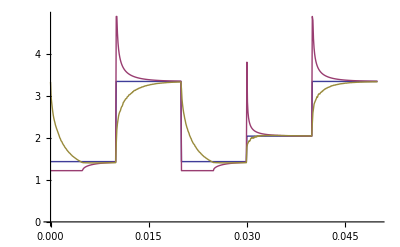

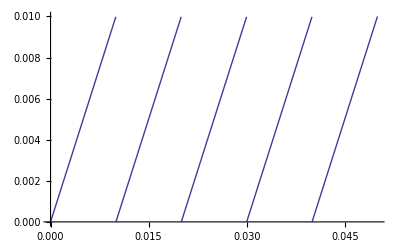

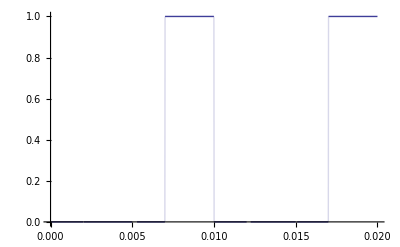

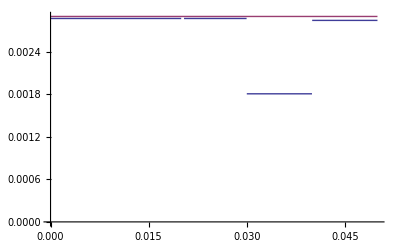

```mathematica
(*Extra Plots*)
Plot[{Vextern[t],Voverdrive[t],Vpixel[t]},{t,0,5/FrameRate},AxesOrigin->{0,0},PlotPoints->10]//Quiet
Plot[FrameTime[t],{t,0,5/FrameRate}]
Plot[DutyWave[FrameRate (t-PersistenceDelay),PersistenceDutyCycle],{t,0,2/FrameRate},AxesOrigin->{0,0},PlotRange->Full,Filling->True]
Plot[{τ[t],PixelSpeed},{t,0,5/FrameRate},AxesOrigin->{0,0}]//Quiet
```